Exercises for Section 31 | Parts of Lists

Find the last 5 digits in 2^1000. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Take[IntegerDigits[2^1000],-5]
```

{6,9,3,7,6}

Pick out letters 10 through 20 in the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Alphabet[][[10;;20]]
```

{j,k,l,m,n,o,p,q,r,s,t}

Make a list of the letters at even-numbered positions in the alphabet. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Alphabet[][[Select[Range[26],EvenQ]]]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

```mathematica
Select[Range[26],EvenQ]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26}

Make a line plot of the second to last digit in the first 100 powers of 12. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Part[IntegerDigits[12^n],-2],{n,100}]]
```

-Graphics-

```mathematica
Array[12^2]
```

{144[1]}

```mathematica
Part[{12^2},1]
```

144

Join lists of the first 20 squares and cubes, and get the 10 smallest elements of the combined list. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TakeSmallest[Join[Table[n^2,{n,20}],Table[k^3,{k,20}]],10]
```

{1,1,4,8,9,16,25,27,36,49}

Find the positions of the word “software” in the Wikipedia entry for “computers”. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
WikidataData["computers"]
```

```mathematica
Flatten@Position[TextWords@WikipediaData["computers"],"software"]
```

{59,5790,5884,5906,6638,6660,6663,6667,6681,7884,7985,7992,8000,8022}

Make a histogram of where the letter “e” occurs in the words in WordList[ ]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Position[TextWords@WordList[],"e"]
```

{}

```mathematica
Position[#,"e"]&/@WordList[]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},38990,{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}
 |  |  |  |

```mathematica
TextWords@WordList[]
```

{{a},{aah},{aardvark},{aback},{abacus},{abaft},{abalone},{abandon},{abandoned},{abandonment},{abase},39154,{zoological},{zoologist},{zoology},{zoom},{zoophyte},{zounds},{zucchini},{zwieback},{zydeco},{zygote},{zygotic}}
 |  |  |  |

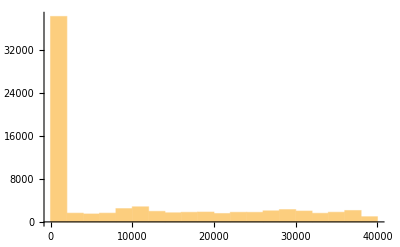

```mathematica
Histogram@Flatten@Position[Characters /@ WordList[], "e"]
```

Make a list of the first 100 cubes, with every one whose position is a square replaced by Red. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ReplacePart[{a, b, c, d, e, f, g}, 3 -> x]
```

{a,b,x,d,e,f,g}

```mathematica
ReplacePart[Table[n^3,{n,100}],1->Red]
```

{RGBColor[1, 0, 0],8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000,9261,10648,12167,13824,15625,17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,46656,50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,117649,125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,262144,274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,531441,551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,1000000}

```mathematica
If[Table[IntegerDigits[#][[n]]==1,{n,Length[IntegerDigits[#]]}],Red,#]&/@Table[n^3,{n,100}];
```

```mathematica
IntegerDigits[#]&/@Table[n^3,{n,10}]
```

{{1},{8},{2,7},{6,4},{1,2,5},{2,1,6},{3,4,3},{5,1,2},{7,2,9},{1,0,0,0}}

```mathematica
ReplacePart[Table[n^3, {n, 100}], Thread[Table[n^2, {n, 100}] -> Red]]
```

{RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]}

Make a list of the first 100 primes, dropping ones whose first digit is less than 5. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
If[First[IntegerDigits[#]]<5,Nothing,#]&/@Array[Prime,100]
```

{5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541}

Make a grid starting with Range[10], then at each of 9 steps randomly removing another element. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Grid[Table[Table[Range[n],{n,{10,k}}],{k,1}]]
```

{1,2,3,4,5,6,7,8,9,10} | {1}

```mathematica
Table[Range[n],{n,10}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
Grid@NestList[ReplacePart[#, RandomInteger[{1, Length[#]}] -> Nothing] &, 
 Range[10], 9]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 
1 | 2 | 4 | 5 | 6 | 7 | 9 | 10 |  | 
2 | 4 | 5 | 6 | 7 | 9 | 10 |  |  | 
2 | 4 | 6 | 7 | 9 | 10 |  |  |  | 
2 | 4 | 6 | 7 | 10 |  |  |  |  | 
2 | 4 | 6 | 7 |  |  |  |  |  | 
2 | 4 | 7 |  |  |  |  |  |  | 
2 | 4 |  |  |  |  |  |  |  | 
2 |  |  |  |  |  |  |  |  |

Find the longest 10 words in WordList[ ]. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TakeLargest[#,StringLength/@#,10]&/@WordList[]
```

TakeLargest::nonopt: Options expected (instead of 10) beyond position 2 in TakeLargest[a,a,10]. An option must be a rule or a list of rules.

TakeLargest::nonopt: Options expected (instead of 10) beyond position 2 in TakeLargest[aah,aah,10]. An option must be a rule or a list of rules.

TakeLargest::nonopt: Options expected (instead of 10) beyond position 2 in TakeLargest[aardvark,aardvark,10]. An option must be a rule or a list of rules.

General::stop: Further output of TakeLargest::nonopt will be suppressed during this calculation.

{TakeLargest[a,a,10],TakeLargest[aah,aah,10],TakeLargest[aardvark,aardvark,10],TakeLargest[aback,aback,10],39168,TakeLargest[zwieback,zwieback,10],TakeLargest[zydeco,zydeco,10],TakeLargest[zygote,zygote,10],TakeLargest[zygotic,zygotic,10]}
 |  |  |  |

```mathematica
Select[WordList[],StringLength[]]
```

{1,3,8,5,6,5,7,7,9,11,5,9,5,7,9,5,9,8,4,6,5,5,10,11,12,8,10,7,9,6,9,9,8,5,4,8,10,4,7,8,5,10,9,8,5,7,7,6,9,8,10,6,6,7,8,8,6,4,6,8,4,8,10,8,11,10,39045,9,7,4,5,5,3,5,6,4,4,3,6,4,6,8,7,9,5,4,3,6,6,8,4,6,4,7,9,5,4,6,6,5,7,4,9,4,6,6,3,6,5,6,9,3,6,5,6,8,6,5,4,6,3,10,9,7,4,8,6,8,8,6,6,7}
 |  |  |  |

```mathematica
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,counterrevolutionary,buckminsterfullerene,compartmentalization,electroencephalogram,internationalization,uncharacteristically,magnetohydrodynamics,incomprehensibility}

Find the 5 longest integer names for integers up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
TakeLargestBy[IntegerName/@Table[n,{n,100}],StringLength,5]
```

{seventy-seven,seventy-three,seventy-eight,twenty-three,twenty-eight}

Find the 5 English names for integers up to 100 that have the largest number of “e”s in them. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
IntegerName/@Table[n,{n,100}]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

```mathematica
TakeLargestBy[IntegerName/@Table[n,{n,100}],Count[Characters[#],"e"]&,5]
```

{seventy-three,seventeen,seventy-seven,nineteen,eleven}

```mathematica
IntegerName/@Table[n,{n,100}]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}